```mathematica
(*2BBM-4.B-10ns-100.0ns and 2BBM-23.B-10ns-100.0ns FFCF and SolEFP breakdwon*)
(*Does FFCF in a slow way. If you have multiple FFCFs to calculate, use slv_calc-tcf-mod in folder FFCF*)
(*Run solefp-analysis.nb first*)
spacing = 40 (*fs*);
```

```mathematica
(*FFCF*)
W4CFFCF=Table[{delay*spacing,CorrelationFunction[W4CAddChonhmeFreq,delay]},{delay,0,20000,1}];
```

```mathematica
S23CFFCF=Table[{delay*spacing,CorrelationFunction[S23CAddChonhmeFreq,delay]},{delay,0,20000,1}];
```

```mathematica
SetDirectory["/Users/Sherina/Desktop"];
W4CFFCFRaw=Import["W4CFFCF.txt","Table"];
S23CFFCFRaw=Import["S23CFFCF.txt","Table"];
(*Correction for number of data points in average (See MM' definition for CorrelationFunction!*)
W4CFFCF=Table[{W4CFFCFRaw[[i,1]],W4CFFCFRaw[[i,2]]*250001/(250001-(i-1))},{i,1,20001}];
S23CFFCF=Table[{S23CFFCFRaw[[i,1]],S23CFFCFRaw[[i,2]]*250001/(250001-(i-1))},{i,1,20001}];
```

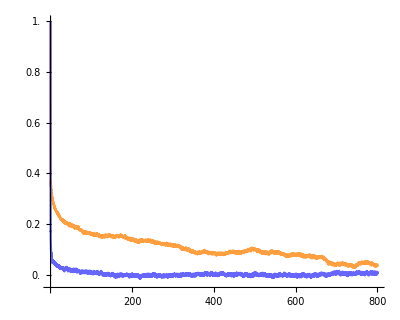

```mathematica
(*Plot*)
ListPlot[{Table[{W4CFFCF[[i,1]]/1000,W4CFFCF[[i,2]]},{i,1,20000}],Table[{S23CFFCF[[i,1]]/1000,S23CFFCF[[i,2]]},{i,1,20000}]},Joined-> True,PlotStyle->{Lighter[Orange,0.25],Lighter[Blue,0.4]},PlotRange-> {{0,800},{-0.05,1}},AspectRatio->0.8,AxesStyle-> Directive[Black,FontSize-> 18,Thickness-> 0.005],Ticks-> {Table[i,{i,200,800,200}],Table[i,{i,0,1,0.2}]},TicksStyle->Directive[Black,FontSize-> 18,Thickness-> 0.005],AxesOrigin->{0,-0.05}]
```

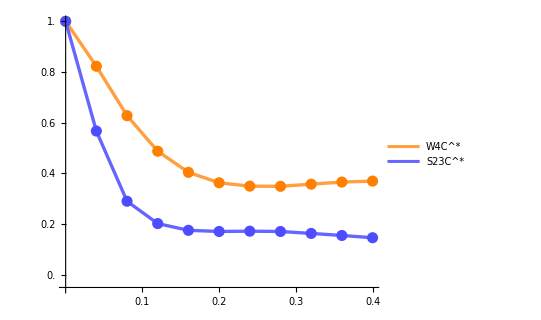

```mathematica
(*Zoom in on short time range*)
Show[ListPlot[{Table[{W4CFFCF[[i,1]]/1000,W4CFFCF[[i,2]]},{i,1,11}],Table[{S23CFFCF[[i,1]]/1000,S23CFFCF[[i,2]]},{i,1,11}]},Joined->True,PlotStyle->{{Lighter[Orange,0.25],Thickness[0.006]},{Lighter[Blue,0.4],Thickness[0.006]}},PlotRange-> {{0,0.4},{-0.05,1}},AspectRatio->0.8,AxesStyle-> Directive[Black,FontSize-> 18,Thickness-> 0.008],Ticks-> {Table[i,{i,0.1,0.4,0.1}],Table[i,{i,0,1,0.2}]},TicksStyle->Directive[Black,FontSize-> 24,Thickness-> 0.008],AxesOrigin->{0,-0.05},PlotLegends-> {"W4C^*","S23C^*"} ],ListPlot[{Table[{W4CFFCF[[i,1]]/1000,W4CFFCF[[i,2]]},{i,1,11}],Table[{S23CFFCF[[i,1]]/1000,S23CFFCF[[i,2]]},{i,1,11}]},PlotStyle->{{Orange,PointSize[0.02]},{Lighter[Blue,0.3],PointSize[0.02]}},PlotRange-> {{0,0.4},{-0.05,1}},AspectRatio->0.8,AxesStyle-> Directive[Black,FontSize-> 18,Thickness-> 0.008],Ticks-> {Table[i,{i,0.1,0.4,0.1}],Table[i,{i,0,1,0.2}]},TicksStyle->Directive[Black,FontSize-> 24,Thickness-> 0.008],AxesOrigin->{0,-0.05}]]
```

```mathematica
(*variance and tau_c*)
deltaW4C=Sqrt[Variance[W4CAddChonhmeFreq]*250000/250001](*cm^-1*)*2.997913*10^10(*s^-1/cm-1*)*1/10^12(*s/ps*);
deltaS23C=Sqrt[Variance[S23CAddChonhmeFreq]*250000/250001](*cm^-1*)*2.997913*10^10(*s^-1/cm-1*)*1/10^12(*s/ps*);
```

```mathematica
tauW4C=Total[W4CFFCF[[;;,2]]]*40(*fs*)*1/1000(*ps/fs*);
tauS23C=Total[S23CFFCF[[;;,2]]]*40(*fs*)*1/1000(*ps/fs*);
```

```mathematica
deltatauW4C=deltaW4C*tauW4C;
deltatauS23C=deltaS23C*tauS23C;
```

```mathematica
(*Table*)
TableForm[{{deltaW4C,tauW4C,deltatauW4C},{deltaS23C,tauS23C,deltatauS23C}},TableHeadings->{{"W4C^*","S23C^*"},{"Δ (ps^-1)","τ (ps)","Δτ"}}]
```

| Δ (ps^-1) | τ (ps) | Δτ
W4C^* | 0.269378 | 86.6432 | 23.3397
S23C^* | 0.413153 | 2.99083 | 1.23567